```mathematica
etafun=η^2+(ω^2-2 ω)(1-η)^2+2 ω^2 Log[η]+2 ω^2(1-η)
```

η^2+2 (1-η) ω^2+(1-η)^2 (-2 ω+ω^2)+2 ω^2 Log[η]

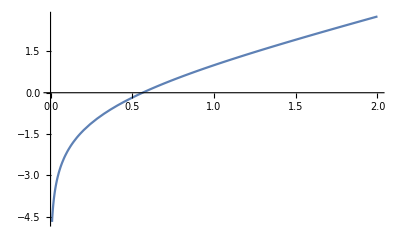

```mathematica
Plot[etafun/.{ω->1/1.4},{η,0,2}]
```

```mathematica
EtaGas=etafun/.{ω->1/κ}//Simplify
EtaGas/.{κ->1.4}
```

(3+4 η (-1+κ)+η^2 (-1+κ)^2-2 κ+2 Log[η])/κ^2

0.510204 (0.2+1.6 η+0.16 η^2+2 Log[η])

```mathematica
FindRoot[(EtaGas/.{κ->1.4})==0,{η,0.5}]
```

{η→0.562519}